```mathematica
latex[x_] := StringReplace[ToString@Format[StandardForm[x],TeXForm], {"<" -> " \\lt ", ">" -> " \\gt "}]
outputHtml[txt_] := Module[{i,s}, 
	i = Import["C:/GitRoot/llio/web/analysis_aa.stm", "String"];
	s = StringReplace[i, "<!--#include file=\"mathematica.dps_analysis\" -->" -> txt];
	Export["C:/GitRoot/llio/web/analysis_aa.html", s, "String"]
]
```

## AutoAttack DPS

```mathematica
cost /: Subscript[cost, AD] = 36
cost /: Subscript[cost, AS] = 33/Quantity["Percent"]
cost /: Subscript[cost, CC] = 50/Quantity["Percent"]
cost /: Subscript[cost, LS] = 44/Quantity["Percent"]
cost /: Subscript[cost, HP5] = 36
```

36

33

50

44

36

```mathematica
dps /: Subscript[dps, n]  = (Subscript[AD, n] + Subscript[bonus, AD]) * Subscript[AS, n]* (1 + Subscript[bonus, AS]) * (1 + Subscript[bonus, CC])
dps /: Subscript[dps, gold]= Subscript[dps, n] /. {Subscript[bonus, AS] -> Subscript[gold, AS]/Subscript[cost, AS], Subscript[bonus, CC] -> Subscript[gold, CC]/Subscript[cost, CC], Subscript[bonus, AD] -> Subscript[gold, AD]/Subscript[cost, AD]}
```

AS_n (AD_n+bonus_AD) (1+bonus_AS) (1+bonus_CC)

AS_n (AD_n+gold_AD/36) (1+gold_AS/3300) (1+gold_CC/5000)

```mathematica
Clear[g,distro,system,dist]
g = Subscript[dps, gold]{Subscript[gold, AS],Subscript[gold, CC],Subscript[gold, AD]}

systemG = {
	HoldForm[Subscript[dist, CC]'[Subscript[gold, AD]] == (g[[3]]/g[[2]] /. {Subscript[gold, CC] -> Subscript[dist, CC][Subscript[gold, AD]]})],
	HoldForm[Subscript[dist, AS]'[Subscript[gold, AD]] == (g[[3]]/g[[1]] /. {Subscript[gold, AS] -> Subscript[dist, AS][Subscript[gold, AD]]})]
	}
{distribution} = DSolve[ReleaseHold[systemG], {Subscript[dist, CC][Subscript[gold, AD]],Subscript[dist, AS][Subscript[gold, AD]]}, Subscript[gold, AD]]
```

{(AS_n (AD_n+gold_AD/36) (1+gold_CC/5000))/3300,(AS_n (AD_n+gold_AD/36) (1+gold_AS/3300))/5000,1/36 AS_n (1+gold_AS/3300) (1+gold_CC/5000)}

{dist_CC'[gold_AD]==(g⟦3⟧/g⟦2⟧/.{gold_CC→dist_CC[gold_AD]}),dist_AS'[gold_AD]==(g⟦3⟧/g⟦1⟧/.{gold_AS→dist_AS[gold_AD]})}

{{dist_CC[gold_AD]→-5000+C[1] (36 AD_n+gold_AD),dist_AS[gold_AD]→-3300+C[2] (36 AD_n+gold_AD)}}

```mathematica
$Assumptions = {Subscript[AD, n] == 0, Subscript[gold, AD] > 0}
systemAS0 = Flatten[{Subscript[dist, AS][Subscript[gold, AD]] == Subscript[gold, AS], Subscript[gold, AS] == 0,  $Assumptions}] //. Flatten[{distribution,C[1] -> 1,C[2] -> 1}]
resultAS0 = ToRules@Reduce[systemAS0, Reals] (* /. ConditionalExpression[v_,expr_] :> Piecewise[{{v,expr}}] *)

systemCC0 = Flatten[{Subscript[dist, CC][Subscript[gold, AD]] == Subscript[gold, CC], Subscript[gold, CC] == 0, $Assumptions}] //. Flatten[{distribution,C[1] -> 1,C[2] -> 1}]
resultCC0 = ToRules@Reduce[systemCC0, Reals] (* /. ConditionalExpression[v_,expr_] :> Piecewise[{{v,expr}}]  *)

threshold1 = N@(Subscript[gold, AD]/Subscript[cost, AD])/. resultAS0
threshold2 = N@(Subscript[gold, AD]/Subscript[cost, AD])/. resultCC0
```

{AD_n==0,gold_AD>0}

{-3300+36 AD_n+gold_AD==gold_AS,gold_AS==0,AD_n==0,gold_AD>0}

{gold_AD→3300,gold_AS→0,AD_n→0}

{-5000+36 AD_n+gold_AD==gold_CC,gold_CC==0,AD_n==0,gold_AD>0}

{gold_AD→5000,gold_CC→0,AD_n→0}

91.6667

138.889

```mathematica
(* TODO: limits *)
rs = Flatten[{distribution, Subscript[AD, n] -> 0, C[1] -> 1, C[2] -> 1}]
Subscript[dist, CC][Subscript[gold, AD]] //. Flatten[{distribution, Subscript[AD, n] -> 0, Subscript[gold, AD] -> 5000 + 5000, C[1] -> 1}]
Subscript[dist, AS][Subscript[gold, AD]] //. Flatten[{distribution, Subscript[AD, n] -> 0, Subscript[gold, AD] -> 6700 + 3300, C[2] -> 1}]
Subscript[dist, CC][Subscript[gold, AD]] == Subscript[gold, AD] - l2 //. rs
Subscript[dist, AS][Subscript[gold, AD]] == Subscript[gold, AD] - l1 //. rs
```

{dist_CC[gold_AD]→-5000+C[1] (36 AD_n+gold_AD),dist_AS[gold_AD]→-3300+C[2] (36 AD_n+gold_AD),AD_n→0,C[1]→1,C[2]→1}

5000

6700

-5000+gold_AD==-l2+gold_AD

-3300+gold_AD==-l1+gold_AD

```mathematica
l1 = Subscript[gold, AD] /. resultAS0;
l2 = Subscript[gold, AD] /. resultCC0;
gdistroRelAD[ad_] := {ad,Max[0,Subscript[dist, AS][Subscript[gold, AD]]],Max[0,Subscript[dist, CC][Subscript[gold, AD]]]} //. Join[distribution, {Subscript[gold, AD] -> ad, C[1] -> 1, C[2] -> 1, Subscript[AD, n] -> 0}]

Clear[dCC,dAD,dAS,para]
parametricDistroEq = Max[0,Subscript[dist, AS][Subscript[gold, AD]]] + Max[0,Subscript[dist, CC][Subscript[gold, AD]]] + Subscript[gold, AD] == u
goldADofU = Subscript[gold, AD] /. Solve[{Subscript[gold, AD] >= 0, parametricDistroEq} //. rs, Subscript[gold, AD], Reals, MaxExtraConditions->All]
% /. ConditionalExpression[e_,c_] :> 
 	ConditionalExpression[
 	{e, Max[0, Subscript[dist, AS][Subscript[gold, AD]]], Max[0, Subscript[dist, CC][Subscript[gold, AD]]]} //. 
		Append[distribution, Subscript[gold, AD] -> e], c];
% //. {C[1] -> 1, C[2] -> 1};
gdistroset = FullSimplify[%];
conditionalSetToPiecewise[expr_, default_] := Piecewise[expr /. ConditionalExpression[e_,c_] :> {e,c}, default]
gdistro  = conditionalSetToPiecewise[gdistroset, {}]
gdistroD = conditionalSetToPiecewise[D[gdistroset,u], {}]

(*
dAD[h_] := xxx(*&Piecewise[xxx /. ConditionalExpression[e_,c_] :> {e,c}, 0] /. u -> h*)
dCC[h_] := Max[0, Subscript[dist, CC][Subscript[gold, AD]] //. Flatten[{distribution, C[1] -> 1, C[2] -> 1, Subscript[gold, AD] -> dAD[h]}]]
dAS[h_] := Max[0, Subscript[dist, AS][Subscript[gold, AD]] //. Flatten[{distribution, C[1] -> 1, C[2] -> 1, Subscript[gold, AD] -> dAD[h]}]]
*)
(*
para[h_] := {Subscript[gold, AD] -> dAD[h], Subscript[gold, AS] -> dAS[h], Subscript[gold, CC] -> dCC[h]}
paraDPS[h_] := Subscript[dps, gold] /. {Subscript[gold, AD] -> dAD[h], Subscript[gold, AS] -> dAS[h], Subscript[gold, CC] -> dCC[h]}
Plot[{dAD'[h],dAS'[h],dCC'[h]}, {h,0,30000}, PlotRange->{{0,30000},{0,2}}, PlotStyle -> {Directive[Black, Thick], 
				  Directive[Dashed, Red, Thickness[0.015]], 
				  Directive[Blue, Thickness[0.015], Dashing["Large"]],
				  Directive[Green, Thickness[0.015], Dashing["Lage"]]}]
*)
```

Max[0,dist_AS[gold_AD]]+Max[0,dist_CC[gold_AD]]+gold_AD==u

{ConditionalExpression[u,0≤u≤3300],ConditionalExpression[(3300+u)/2,3300<u≤6700],ConditionalExpression[(8300+u)/3,u>6700]}

Piecewise[{{{u,0,0}, 0≤u≤3300}, {{(3300+u)/2,1/2 (-3300+u),0}, 3300<u≤6700}, {{(8300+u)/3,1/3 (-1600+u),1/3 (-6700+u)}, u>6700}, {{}, True}}]

Piecewise[{{{1,0,0}, 0≤u≤3300}, {{1/2,1/2,0}, 3300<u≤6700}, {{1/3,1/3,1/3}, u>6700}, {{}, True}}]

```mathematica
r = 25000;
step = 5000;
(*
data = Flatten[Table[{x,y,z,Subscript[dps, gold]} //. {Subscript[AS, n]->1,Subscript[CC, n]->0,Subscript[AD, n]->50,Subscript[gold, AS]->x,Subscript[gold, CC]->y,Subscript[gold, AD]->z}, {x,0,r,step}, {y,0,r,step}, {z, 0, r, step}], 2];
*)
ascentPath = ParametricPlot3D[gdistro /. {a_,b_,c_} :> {b,c,a} , {u,0,30000}, 
	AxesLabel-> {"Aspd (gold)","Crit (gold)","AD (gold)"},
	PlotStyle->Directive[Thickness[0.0025],RGBColor[16^^FF,0,16^^66,1]], 
	Background->None,
	ViewCenter -> {1/2,1/2,1/2},
	ViewPoint -> {1.4,2,0.4}, 
	ViewVertical->{0.4,0.7,0.9}];

colors[x_] := Blend[{{0, Opacity[1,Darker[Blue]]}, {0.5, Opacity[1,Yellow]}, {1, Opacity[1,Red]}}, x] /.  
	(RGBColor[r_,g_,b_,a_] :> RGBColor[1-r,1-g,1-b,a])

dpsContour = ContourPlot3D[{Subscript[dps, gold]} //. {Subscript[AS, n]->1,Subscript[CC, n]->0,Subscript[AD, n]->50,Subscript[gold, AS]->x,Subscript[gold, CC]->y,Subscript[gold, AD]->z}, {x,0,r},{y,0,r},{z,0,r}, 
	PlotPoints -> 30, MaxRecursion-> 0, Contours -> 150, 
	Mesh -> None,
    Background->None,
	ContourStyle -> Opacity[0.5],
	ColorFunctionScaling  -> True,
	ColorFunction -> Function[{x, y, z, f}, ColorData["BlueGreenYellow"][f]], 
	RegionFunction-> Function[{x,y,z}, x + y + z ≤ r] ];
(*ColorData["AvocadoColors"][f]*)

(*Blend[{{0, Opacity[0.1,Darker[Blue]]}, {800, Opacity[0.2,Yellow]}, {1500, Opacity[0.5,Red]}}, 1000] /. (RGBColor[r_,g_,b_,a_] :> RGBColor[1-r,1-g,1-b,a])*)



thresholdPoints = {0,resultAS0[[1]][[2]],resultCC0[[1]][[2]]}
label[p_,i_] := {
	Graphics3D[Text[ToString[First@i], {-200,-200,800}+p, BaseStyle -> {White, FontSize -> 12, FontFamily -> "Arial"}]],
	Graphics3D[{PointSize[0.008],Red, Point[p]}]
	}

ascentLabeled = Show@@Join[{ascentPath,MapIndexed[label[gdistroRelAD[#1][[{2,3,1}]],#2]&, thresholdPoints]}];
	
(*
dpsGraph = ListPointPlot3D[List /@ data[[All, {1, 2, 3}]], 
 RegionFunction-> Function[{x,y,z}, x + y + z ≤ r],
 PlotStyle -> ({PointSize[Large], 
      colors[#1] } & /@ Flatten[data[[All, {4}]]])];
*)
dpsCombinedGraph = Show[dpsContour,ascentLabeled,
	AxesLabel-> {"Aspd (gold)","Crit (gold)","AD (gold)"},
	Boxed -> True,
	BoxStyle -> Directive[Dotted], 
    Background->None, 
    AxesStyle-> colors[2200] /. (RGBColor[r_,g_,b_,a_] :> RGBColor[r,g,b,1]),
	BoxStyle->White,
	TicksStyle -> White,
	LabelStyle -> Red,

	BaseStyle -> {FontWeight -> "Bold", FontSize -> 14, FontFamily -> "Terminal"},
	BoxRatios->{1,1,0.5},
(*PlotRangePadding -> 0,*)
	ViewCenter -> {1/2,1/2,1/2},
	ImageSize->{500,250},
ViewPoint->{1.7972063735309383,-1.6968044029869762,0.4978340424036346},ViewVertical->{0.6628884964370287,-0.6258227717806889,0.8220090014402306}
]
```

{0,3300,5000}

-Graphics3D-

```mathematica
fileGraphDPS = "images/llio_dps_contour.png"
Export["D:\\GitRoot\\llio\\web\\" <> fileGraphDPS, dpsCombinedGraph, Background -> None, ImageSize->{250*2,250}, BoxRatios->{1,1,1}]
```

images/llio_dps_contour.png

Export::nodir: Directory "D:\\GitRoot\\llio\\web\\images\\" does not exist.

Export::noopen: Cannot open "D:\\GitRoot\\llio\\web\\images/llio_dps_contour.png".

$Failed

```mathematica
Options[-Graphics3D-]
Options[-Graphics3D-]
```

{Axes→True,AxesLabel→{Aspd (gold),Crit (gold),AD (gold)},AxesStyle→RGBColor[0,NCache[5/9,0.555556],1,1],Background→GrayLevel[0],BaseStyle→{FontWeight→Bold,FontSize→14,FontFamily→Terminal},BoxRatios→{1,1,0.4},BoxStyle→Directive[Dashing[{0,Small}]],Boxed→True,ImageSize→{750.374,254.},LabelStyle→RGBColor[1,0,0],PlotRange→{{0,25000},{0,25000},Automatic},PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]},{Automatic,Automatic}},TicksStyle→GrayLevel[1],ViewCenter→{1/2,1/2,1/2},ViewPoint→{1.38042,2.05036,0.102253},ViewVertical→{0.528124,0.791262,0.770506}}

{Axes→True,AxesLabel→{Aspd (gold),Crit (gold),AD (gold)},AxesStyle→RGBColor[0,1,1,1],Background→GrayLevel[0],BaseStyle→{FontWeight→Bold,FontSize→14,FontFamily→Terminal},BoxRatios→{1,1,0.5},BoxStyle→Directive[Dashing[{0,Small}]],Boxed→True,ImageSize→{1500,500},LabelStyle→RGBColor[1,0,0],Lighting→Neutral,Method→{},PlotRange→{{0,25000},{0,25000},{0,25000}},PlotRangePadding→{Scaled[0.02],Scaled[0.02],Scaled[0.02]},TicksStyle→GrayLevel[1],ViewCenter→{1/2,1/2,1/2},ViewPoint→{1.97529,-1.56689,0.00390671},ViewVertical→{0.763848,-0.605122,0.448838}}

```mathematica
costswtf = StringReplace[ToString[{Subscript[cost, AD],Subscript[cost, AS],Subscript[cost, CC]}], "reciprocal percent" -> "/ %"]
html = "</div>
		<div class='analysis_page'>
		<h3> Optimal gold allocation </h3>

		
        <img src='" <> fileGraphDPS <> "'>

		<ul>
		<li> If AD < "<> ToString@threshold1 <>": all gold should be spent to increase AD. </li>
		<li> If " <> ToString@threshold1 <> " < AD < " <> ToString@threshold2 <> ": all gold should be evenly divided between AS and AD. </li>
		<li> If " <> ToString@threshold2 <> " < AD: all gold should be evenly divided between AD/AS/CC until AS and CC reach their hard limits </li>
		</ul>
		Assuming:
		<ul type='square'>
        <li> Gold cost per stat: {AD,AS,CC}=" <> costswtf <> "  </li>
		<li> Critical hit damage bonus: 200% </li>
		</ul>
		
		
		<br>
        </div>

        <div class='analysis_page'>
		<h1> Proof </h1>
		<p>
		Assuming that DPS is calculated as:
        $$ DPS_N = " <> latex[Subscript[dps, n]] <> " $$
        $$AD_n = {base}_{AD} + (n-1) \\cdot {perLV}_{AD}$$
        $$AS_n = {base}_{AS} + (n-1) \\cdot {perLV}_{AS}$$
        $$AD = \\text{attack damage}, AS = \\text{attack speed}, CC = \\text{critical hit chance.}$$
        <br>
        <br>
        Assuming that a unit increase of each stat costs: 
        $$cost_{\\{AD,AS,CC\\}} = " <> latex[{Subscript[cost, AD],Subscript[cost, AS],Subscript[cost, CC]}] <> " $$
        <br>  
        We have dps as a function of gold spent:
        $$DPS_{gold} = " <> latex[Subscript[dps, gold]] <> " $$
        <br>
        Note that the DPS function increases monotonically, so it does not have any extrema.
        </p>
        
        <h3> Optimal gold allocation </h3>
		<p>
       
        Since we are interested in maximizing our DPS per gold spent, i.e. finding the greatest rate of change, 
		and our DPS function is differentiable, the relationship between the input variables and output DPS
		can be found by taking the gradient of the function, using vector calculus.
        $$ g = \\nabla dps_{gold} = \\{dps'_{{gold}_{(gold_{AS})}},dps'_{{gold}_{(gold_{CC})}},dps'_{{gold}_{(gold_{AD})}} \\}$$
        $$ g_1 = " <> latex[g[[1]]] <> " $$
        $$ g_2 = " <> latex[g[[2]]] <> " $$
        $$ g_3 = " <> latex[g[[3]]] <> " $$
        <br>

		Since 'the gradient points in the direction of the greatest rate of increase of the function and its magnitude is the slope of the graph in that direction', 
		the set of points, corresponding to the optimal distributions of gold, is equivalent to the path of steepest ascent on the surface defined by our function. 
		Consequently we find the optimal amount of gold spent on CC and AS, <strong>relative to AD</strong>, by solving the differential system (where /. indicates pattern substitution):
        " <> Fold[#1 <> "$$ " <> latex[#2 //. (Part[g_,i_Integer] :> Subscript[g, i])] <> " $$\n"&, "",systemG] <> "
        yields: 
		$$ " <> latex@distribution[[1]] <> " $$ 
		$$ " <> latex@distribution[[2]] <> " $$ 
		</p>

        <h4>Piecewise intervals</h4>
		<p>
		Clearly, attack speed and crit chance have negative utility when AD levels are low, 
		and since our value of gold spent can't be negative, we need to find the points where they cross zero,
		using them to define seperate intervals.
		<br>
        <br>
		For attack speed we reduce: 
		" <> Fold[#1 <> "$$ " <> latex[#2] <> " $$\n"&, "", systemAS0] <> "
		yielding:
		$$ " <> latex[resultAS0] <> " $$
        <br>

		And for critical hit chance we reduce: 
		" <> Fold[#1 <> "$$ " <> latex[#2] <> " $$\n"&, "", systemCC0] <> "
		yielding:
		$$ " <> latex[resultCC0] <> " $$
        <br>
		Note that we've seen these values before in our algebraic analysis.
		$$ " <> latex[{Subscript[gold, AD]== N@(Subscript[gold, AD]/Subscript[cost, AD])AD /. resultAS0, Subscript[gold, AD] == N@(Subscript[gold, AD]/Subscript[cost, AD]) AD /. resultCC0 }] <> " $$
		</p>

        <h4>Conclusions</h4>
        <p>
		At this point we can draw our initially stated conclusions, simply by looking at the functions, 
		but to further clarify our point we define a new function: 
		$$ f(u)=" <> latex[{Subscript[gold, AD][u],Subscript[dist, AS][Subscript[gold, AD][u]],Subscript[dist, CC][Subscript[gold, AD][u]]}] <> " $$
        <br>
		by solving for gold_AD(u) in:
		$$ " <> latex[parametricDistroEq] <> " $$
		resulting in:
		<br><br>
		$$ gold_{AD}(u)=" <> latex[conditionalSetToPiecewise[goldADofU,0]] <> "$$
        <br><br>
		substituting it back into f(u) yields:
		<br><br>
		$$ f(u)=" <> latex[gdistro] <> "$$
        <br><br>
		taking the first derivative, we see how gold is best divided during each interval:
		<br><br>
		$$ f'(u)=" <> latex[gdistroD] <> "$$
		</p>
	";
(*Fold[#1 <> "gold_{AD}(u)=" <> latex[#2] <> "\\\\"&, "", goldADofU]*)
outputHtml[html]
```

{36, 33 / %, 50 / %}

Part::pspec: Part specification i_Integer is neither a machine-sized integer nor a list of machine-sized integers.

C:/GitRoot/llio/web/analysis_aa.html

## Sustain analysis

```mathematica
sustain /: Subscript[sustain, n] = (Subscript[dps, n]  Min[1,Subscript[bonus, LS]]) + Subscript[bonus, HP5]/5
sustain /: Subscript[sustain, gold] = (Subscript[dps, gold]  Subscript[gold, LS]/Subscript[cost, LS]) + (Subscript[gold, HP5]/Subscript[cost, HP5])/5
```

Min[1,bonus_LS] AS_n (AD_n+bonus_AD) (1+bonus_AS) (1+bonus_CC)+bonus_HP5/5

gold_HP5/180+(AS_n (AD_n+gold_AD/36) (1+gold_AS/3300) (1+gold_CC/5000) gold_LS)/4400

```mathematica
sustainVars = {Subscript[gold, AD],Subscript[gold, AS],Subscript[gold, CC],Subscript[gold, LS],Subscript[gold, HP5]}
sustainGrad = Grad[Subscript[sustain, gold]/. {Subscript[AS, n] -> 1,Subscript[AD, n] -> 0}, sustainVars]

Factor@DSolve[{distCC'[x] == (sustainGrad[[1]]/sustainGrad[[3]] /. {Subscript[gold, AD] -> x, Subscript[gold, CC] -> distCC[x]}), distCC[5300] == 300}, distCC[x],x]
FullSimplify@DSolve[{distLS'[x] == (sustainGrad[[1]]/sustainGrad[[4]] /. {Subscript[gold, AD] -> x, Subscript[gold, LS] -> distLS[x]}), distLS[2500] == 2500}, distLS[x], x]
FullSimplify@DSolve[{distAS'[x] == (sustainGrad[[1]]/sustainGrad[[2]] /. {Subscript[gold, AD] -> x, Subscript[gold, AS] -> distAS[x]}), distAS[6300] == 3000}, distAS[x], x]
```

{gold_AD,gold_AS,gold_CC,gold_LS,gold_HP5}

{((1+gold_AS/3300) (1+gold_CC/5000) gold_LS)/158400,(gold_AD (1+gold_CC/5000) gold_LS)/522720000,(gold_AD (1+gold_AS/3300) gold_LS)/792000000,(gold_AD (1+gold_AS/3300) (1+gold_CC/5000))/158400,1/180}

{{distCC[x]→-5000+x}}

{{distLS[x]→x}}

{{distAS[x]→-3300+x}}

```mathematica
sustainGrad2 = Grad[Subscript[sustain, gold], sustainVars]

sustainCC1 = DSolve[{distCC'[x] == (sustainGrad2[[3]]/sustainGrad2[[1]] /. {Subscript[gold, AD] -> x, Subscript[gold, CC] -> distCC[x]}), distCC[5000] == (Subscript[cost, AD] * Subscript[AD, n])}, distCC[x],x]
sustainLS1 = DSolve[{distLS'[x] == (sustainGrad2[[4]]/sustainGrad2[[1]] /. {Subscript[gold, AD] -> x, Subscript[gold, LS] -> distLS[x]}), distLS[0] == (Subscript[cost, AD] * Subscript[AD, n])}, distLS[x], x]
sustainAS1 = DSolve[{distAS'[x] == (sustainGrad2[[2]]/sustainGrad2[[1]] /. {Subscript[gold, AD] -> x, Subscript[gold, AS] -> distAS[x]}), distAS[3300] == (Subscript[cost, AD] * Subscript[AD, n])}, distAS[x], x]
sustainRules1 = Assuming[{x≥ 0, Subscript[AD, n] ≥ 0}, Flatten@FullSimplify[{sustainCC1[[2]],sustainLS1[[2]],sustainAS1[[2]]}]]
sustainRules = FullSimplify@Thread[{Subscript[gold, AS],Subscript[gold, LS],Subscript[gold, CC]} -> {distAS[x],distLS[x],distCC[x]} /. %]/. x -> Subscript[gold, AD]
sustainAds = {
	{Subscript[gold, AD] + Subscript[gold, AS] + Subscript[gold, LS] + Subscript[gold, CC] == u, 0 ≥ Subscript[gold, CC]},
	{Subscript[gold, AD] + Subscript[gold, AS] + Subscript[gold, LS] == u, 0 ≥ Subscript[gold, AS]},
	{Subscript[gold, AD] + Subscript[gold, LS] == u, 0 ≥ Subscript[gold, AD]}
	(*ConditionalExpression[Subscript[gold, LS] == u, 0 ≥ Subscript[gold, LS]]*)
} /. sustainRules
sustainAds2 = Flatten[Solve[#[[1]], Subscript[gold, AD], Reals, MaxExtraConditions->Infinity]& /@ sustainAds] 
sustainIntervals = {
	{Subscript[gold, AS] -> distAS[x], Subscript[gold, LS] -> distLS[x], Subscript[gold, CC] -> distCC[x]},
	{Subscript[gold, AS] -> distAS[x], Subscript[gold, LS] -> distLS[x], Subscript[gold, CC] -> 0},
	{Subscript[gold, AS] -> 0, Subscript[gold, LS] -> distLS[x], Subscript[gold, CC] -> 0}
} /. sustainRules1 /. x -> Subscript[gold, AD] 
Map[{Prepend[#[[1]] /. #[[2]],#[[2]]],#[[3]][[2]]}&,Thread[{sustainIntervals,sustainAds2,sustainAds}]] // TableForm
distSustain = Piecewise[%,{}]
(*sustainRulesAD = Subscript[gold, AD] -> Piecewise[(% /. ((Subscript[gold, AD] -> ConditionalExpression[a_,b_]) :> {a,b})), 0]*)
"=="
```

{(AS_n (1+gold_AS/3300) (1+gold_CC/5000) gold_LS)/158400,(AS_n (AD_n+gold_AD/36) (1+gold_CC/5000) gold_LS)/14520000,(AS_n (AD_n+gold_AD/36) (1+gold_AS/3300) gold_LS)/22000000,(AS_n (AD_n+gold_AD/36) (1+gold_AS/3300) (1+gold_CC/5000))/4400,1/180}

{{distCC[x]→-5000-√((x+36 AD_n)^2)},{distCC[x]→-5000+√((x+36 AD_n)^2)}}

{{distLS[x]→-√((x+36 AD_n)^2)},{distLS[x]→√((x+36 AD_n)^2)}}

{{distAS[x]→-3300-√((x+36 AD_n)^2)},{distAS[x]→-3300+√((x+36 AD_n)^2)}}

{distCC[x]→-5000+x+36 AD_n,distLS[x]→x+36 AD_n,distAS[x]→-3300+x+36 AD_n}

{gold_AS→-3300+36 AD_n+gold_AD,gold_LS→36 AD_n+gold_AD,gold_CC→-5000+36 AD_n+gold_AD}

{{-8300+108 AD_n+4 gold_AD==u,0≥-5000+36 AD_n+gold_AD},{-3300+72 AD_n+3 gold_AD==u,0≥-3300+36 AD_n+gold_AD},{36 AD_n+2 gold_AD==u,0≥gold_AD}}

{gold_AD→2075+u/4-27 AD_n,gold_AD→1100+u/3-24 AD_n,gold_AD→u/2-18 AD_n}

{{gold_AS→-3300+36 AD_n+gold_AD,gold_LS→36 AD_n+gold_AD,gold_CC→-5000+36 AD_n+gold_AD},{gold_AS→-3300+36 AD_n+gold_AD,gold_LS→36 AD_n+gold_AD,gold_CC→0},{gold_AS→0,gold_LS→36 AD_n+gold_AD,gold_CC→0}}

gold_AD→2075+u/4-27 AD_n
gold_AS→-1225+u/4+9 AD_n
gold_LS→2075+u/4+9 AD_n
gold_CC→-2925+u/4+9 AD_n | 0≥-5000+36 AD_n+gold_AD
gold_AD→1100+u/3-24 AD_n
gold_AS→-2200+u/3+12 AD_n
gold_LS→1100+u/3+12 AD_n
gold_CC→0 | 0≥-3300+36 AD_n+gold_AD
gold_AD→u/2-18 AD_n
gold_AS→0
gold_LS→u/2+18 AD_n
gold_CC→0 | 0≥gold_AD

Piecewise[{{{gold_AD→2075+u/4-27 AD_n,gold_AS→-1225+u/4+9 AD_n,gold_LS→2075+u/4+9 AD_n,gold_CC→-2925+u/4+9 AD_n}, 0≥-5000+36 AD_n+gold_AD}, {{gold_AD→1100+u/3-24 AD_n,gold_AS→-2200+u/3+12 AD_n,gold_LS→1100+u/3+12 AD_n,gold_CC→0}, 0≥-3300+36 AD_n+gold_AD}, {{gold_AD→u/2-18 AD_n,gold_AS→0,gold_LS→u/2+18 AD_n,gold_CC→0}, 0≥gold_AD}, {{}, True}}]

==

```mathematica
N[distSustain] /. {Subscript[AD, n] -> minAD, Subscript[AS, n] -> minAS, Subscript[gold, HP5] -> 0, u -> 12000}
```

Piecewise[{{{gold_AD→3860.,gold_AS→2180.,gold_LS→5480.,gold_CC→480.}, 0.≥-3380.+gold_AD}, {{gold_AD→4020.,gold_AS→2340.,gold_LS→5640.,gold_CC→0.}, 0.≥-1680.+gold_AD}, {{gold_AD→5190.,gold_AS→0.,gold_LS→6810.,gold_CC→0.}, 0.≥gold_AD}, {{}, True}}]

```mathematica
HoldForm[(Subscript[dps, gold]  Subscript[gold, LS]/Subscript[cost, LS]) ≤ (Subscript[gold, HP5]/Subscript[cost, HP5])/5]
FullSimplify@Reduce[ReleaseHold[%] /. {Subscript[AS, n] -> 20/60,Subscript[AD, n] -> 45,Subscript[gold, CC] -> 0, Subscript[gold, AS] -> 0, Subscript[gold, AD] ->1/2 (-1620+x), Subscript[gold, LS] -> 1620+(1/2 (-1620+x)), Subscript[gold, HP5] -> x}, Subscript[gold, HP5], Reals]

N@%
3520/36.0
10/60
```

(dps_gold gold_LS)/cost_LS≤gold_HP5/(cost_HP5 5)

60 (61-4 √187)≤x≤60 (61+4 √187)

378.049≤x≤6941.95

97.7778

1/6

```mathematica
minAD = 45
minAS = 20/60
sccsScale = 1000
(*
N@Table[{i*sccsScale/4,{Subscript[sustain, gold] /. {Subscript[AS, n] -> 1,Subscript[AD, n] -> minAD, Subscript[gold, AD] -> 0, Subscript[gold, LS] -> 0, Subscript[gold, CC] -> 0, Subscript[gold, AS] -> 0, Subscript[gold, HP5] -> i*sccsScale/4},{Subscript[gold, AD] -> 0, Subscript[gold, LS] -> 0, Subscript[gold, CC] -> 0, Subscript[gold, AS] -> 0, Subscript[gold, HP5] -> i*sccsScale/4}}}, {i,1,12}];
sustainSamples1 = Join[%,Table[{i*sccsScale,Maximize[{Subscript[sustain, gold] /. {Subscript[AS, n] -> 1,Subscript[AD, n] -> minAD}, 
	{Thread[sustainVars ≥ 0], Total[sustainVars] == ((i-3)*sccsScale)+(3000*0.7)}}, sustainVars]},{i,3,10}]];
sustainSamples2 = Table[{i*sccsScale,Maximize[{Subscript[sustain, gold] /. {Subscript[AS, n] -> 1,Subscript[AD, n] -> minAD}, 
	{Thread[sustainVars ≥ 0], Subscript[gold, HP5] == 3000, Total[sustainVars] == i*sccsScale}}, sustainVars]},{i,3,10}];*)
sustainSamples3 = Table[{i*sccsScale,Maximize[{Subscript[sustain, gold] /. {Subscript[AS, n] -> minAS,Subscript[AD, n] -> minAD}, 
	{Thread[sustainVars ≥ 0], Subscript[gold, AS] == 0, Total[sustainVars] == i*sccsScale}}, sustainVars]},{i,1,10}];
```

45

1/3

1000

gold_AD→0. | gold_AS→0. | gold_CC→0. | gold_LS→0. | gold_HP5→1000.
gold_AD→0. | gold_AS→0. | gold_CC→0. | gold_LS→0. | gold_HP5→2000.
gold_AD→0. | gold_AS→0. | gold_CC→0. | gold_LS→0. | gold_HP5→3000.
gold_AD→0. | gold_AS→0. | gold_CC→0. | gold_LS→0. | gold_HP5→4000.
gold_AD→0. | gold_AS→0. | gold_CC→0. | gold_LS→0. | gold_HP5→5000.
gold_AD→0. | gold_AS→0. | gold_CC→0. | gold_LS→0. | gold_HP5→6000.
gold_AD→2690. | gold_AS→0. | gold_CC→0. | gold_LS→4310. | gold_HP5→0.
gold_AD→3190. | gold_AS→0. | gold_CC→0. | gold_LS→4810. | gold_HP5→0.
gold_AD→3586.67 | gold_AS→0. | gold_CC→206.667 | gold_LS→5206.67 | gold_HP5→0.
gold_AD→3920. | gold_AS→0. | gold_CC→540. | gold_LS→5540. | gold_HP5→0.

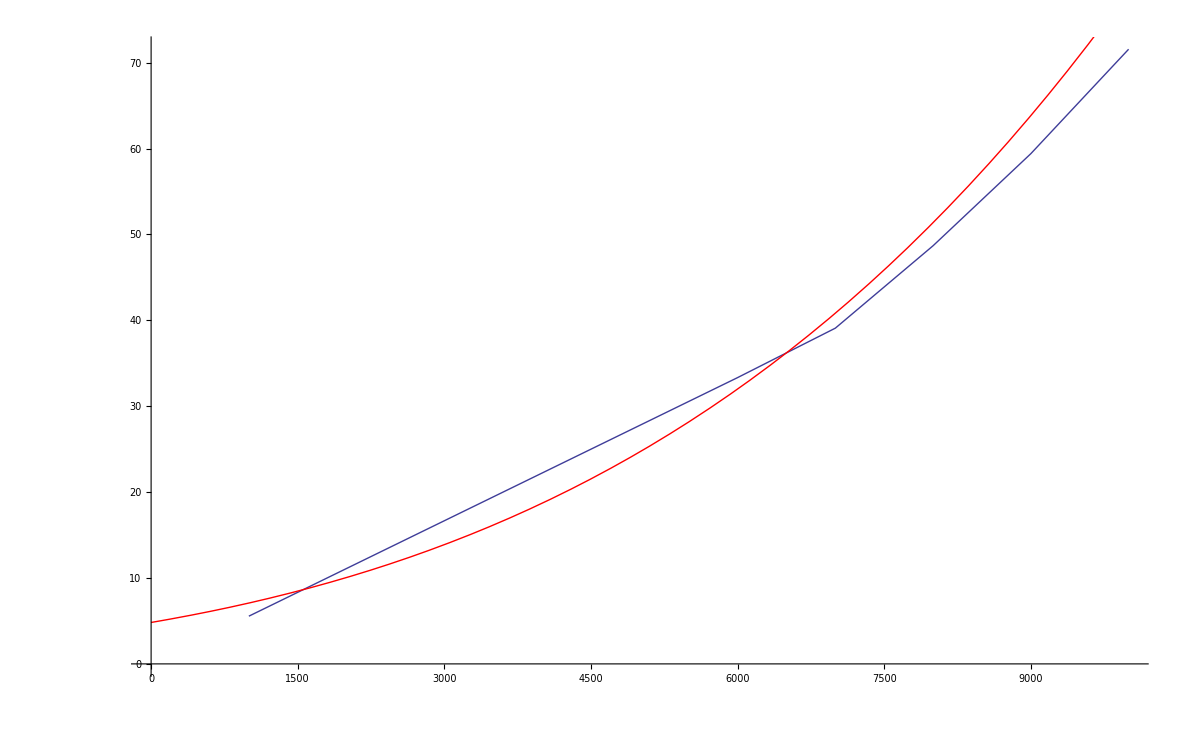

```mathematica
N@sustainSamples3[[All,2,2]] // TableForm


Show[(*
	ListLinePlot[{#[[1]],#[[2]][[1]]}& /@ sustainSamples1],
	ListLinePlot[{#[[1]],#[[2]][[1]]}& /@ sustainSamples2, PlotStyle->Red], *)
	ListLinePlot[{#[[1]],#[[2]][[1]]}& /@ sustainSamples3],
	Plot[PiecewiseExpand[Subscript[sustain, gold] /. distSustain] /. {Subscript[AD, n] -> minAD, Subscript[AS, n] -> minAS, Subscript[gold, HP5] -> 0}, {u,0,10000}, PlotStyle->Red]
]
```

## Defensive stat analysis

### Definitions

Incoming damage is classified according to three different types: 
	- TrueDmg (can’t be mitigated)
	- MagicDmg (reduced by magic resist)
	- PhysicalDmg (reduced by armor)
	
Here we define {scaleAR, scaleMR} to be the percentages of total damage consisting of their respective damage types. 
With [scaleAR + scaleMR <= 1.0] and the amount of TrueDmg being implicitly defined by the remainder of [1.0 - (scaleAR + scaleMR) ]

```mathematica
releaseAllHold[expr_] := 
    Replace[expr, (Hold|HoldForm|HoldPattern|HoldComplete|Defer)[e___] :> e, 
            {0, Infinity}, Heads -> True]

cost /: Subscript[cost, AR] = 20
cost /: Subscript[cost, MR] = 20
cost /: Subscript[cost, HP] = 66/25

dweights = {Subscript[w, P] -> 63/100, Subscript[w, M] -> 36/100, Subscript[w, T] -> 1/100}
dcosts = { Subscript[bonus, AR] -> Subscript[gold, AR]/Subscript[cost, AR], 
		   Subscript[bonus, MR] -> Subscript[gold, MR]/Subscript[cost, MR], 
   		Subscript[bonus, HP] -> Subscript[gold, HP]/Subscript[cost, HP] }

dmgP[HP_,AR_] := HoldForm[HP/(1 - AR/(100 + AR))]

dmgPoly = (Subscript[HP, n] + Subscript[gold, HP]/Subscript[cost, HP]) (63/100(100+Subscript[AR, n]+Subscript[gold, AR]/Subscript[cost, AR])/100 + 36/100(100+Subscript[MR, n]+Subscript[gold, MR]/Subscript[cost, MR])/100+1/100)

(*Hold[Defer@Evaluate[Subscript[dmg, total]]] /. (dweights /. ((x_ -> y_) :> x :> RuleCondition[Defer[y]]))*)
(*
dmgTotal[{wP_,wM_,wT_},dmgP_,dmgM_,dmgT_] := HoldForm[wP dmgP + wM dmgM + wT dmgT]
dmgM[HP_,MR_] := dmgP[HP,MR] 
dmgT[HP_] := HP

dmgTotal[dweights[[All,1]],Subscript[dmg, P],Subscript[dmg, M],Subscript[dmg, T]]
dmgTotal[Defer/@dweights[[All,2]],Subscript[dmg, P],Subscript[dmg, M],Subscript[dmg, T]]
dmgTotal[Defer/@dweights[[All,2]],Defer/@dmgP[HP,AR],Defer/@dmgM[HP,MR],Defer/@dmgT[HP]]
*)

releaseAllHold[%] /. {HP -> 2000, MR -> 0, AR -> 100}

HoldForm[Subscript[w, P] Subscript[dmg, P]+Subscript[w, M] Subscript[dmg, M]+Subscript[w, T] Subscript[dmg, T]]
% /. (dweights /. (Rule[x_,y_] :> x -> Defer[y]))
% /. {Subscript[dmg, P] -> dmgP[HP,AR], Subscript[dmg, M] -> dmgP[HP,MR], Subscript[dmg, T] -> HP}
% /. {HP -> Subscript[HP, n] + Subscript[bonus, HP], AR -> Subscript[AR, n] + Subscript[bonus, AR], MR -> Subscript[MR, n] + Subscript[bonus, MR]}
% /. dcosts
Reduce[releaseAllHold[%] == dmgPoly]
```

20

20

66/25

{w_P→63/100,w_M→9/25,w_T→1/100}

{bonus_AR→gold_AR/20,bonus_MR→gold_MR/20,bonus_HP→(25 gold_HP)/66}

((25 gold_HP)/66+HP_n) (1/100+(63 (100+AR_n+gold_AR/20))/10000+(9 (100+gold_MR/20+MR_n))/2500)

(1/100+(9 (100+0_n+gold_0/20))/2500+(63 (100+100_n+gold_100/20))/10000) (2000_n+(25 gold_2000)/66)

w_P dmg_P+w_M dmg_M+w_T dmg_T

63/100 dmg_P+9/25 dmg_M+1/100 dmg_T

63/100 HP/(1-AR/(100+AR))+9/25 HP/(1-MR/(100+MR))+1/100 HP

63/100 (bonus_HP+HP_n)/(1-(AR_n+bonus_AR)/(100+(AR_n+bonus_AR)))+9/25 (bonus_HP+HP_n)/(1-(bonus_MR+MR_n)/(100+(bonus_MR+MR_n)))+1/100 (bonus_HP+HP_n)

63/100 ((25 gold_HP)/66+HP_n)/(1-(AR_n+gold_AR/20)/(100+(AR_n+gold_AR/20)))+9/25 ((25 gold_HP)/66+HP_n)/(1-(gold_MR/20+MR_n)/(100+(gold_MR/20+MR_n)))+1/100 ((25 gold_HP)/66+HP_n)

True

```mathematica
FullSimplify@Grad[dmgPoly, {Subscript[gold, HP],Subscript[gold, MR],Subscript[gold, AR]}]
mrAdScale = First@First@DSolve[distAR'[Subscript[gold, MR]] == (%[[3]])/(%[[2]]) /. Subscript[gold, AR] -> distAR[Subscript[gold, MR]], distAR[Subscript[gold, MR]], Subscript[gold, MR]]
dmgPoly /. Subscript[gold, AR] -> distAR[Subscript[gold, MR]] /. % /. C[1] -> 0
% /. Subscript[gold, MR] -> 2000/5499 Subscript[gold, DEF]
dmgPoly2 = %;
Reduce[% == (Subscript[HP, n] + Subscript[gold, HP]/Subscript[cost, HP]) (1 + (63/100 Subscript[AR, n] + 36/100 Subscript[MR, n])/100 + Subscript[gold, DEF]/3760)]
```

{(200000+1260 AR_n+63 gold_AR+36 gold_MR+720 MR_n)/528000,(9 ((25 gold_HP)/66+HP_n))/50000,(63 ((25 gold_HP)/66+HP_n))/200000}

distAR[gold_MR]→C[1]+(7 gold_MR)/4

((25 gold_HP)/66+HP_n) (1/100+(63 (100+AR_n+(7 gold_MR)/80))/10000+(9 (100+gold_MR/20+MR_n))/2500)

((25 gold_HP)/66+HP_n) (1/100+(63 (100+AR_n+(175 gold_DEF)/5499))/10000+(9 (100+(100 gold_DEF)/5499+MR_n))/2500)

True

```mathematica
(*
N@% /. {Subscript[HP, n] -> 2000, Subscript[MR, n] -> 0, Subscript[AR, n] -> 100, Subscript[gold, MR] -> 0, Subscript[gold, HP] -> 0, C[1] -> 0 }
N@Maximize[{dmgPoly2  /. {Subscript[AR, n] -> 0,Subscript[HP, n] -> 0,Subscript[MR, n] -> 0},Subscript[gold, HP] ≥ 0, Subscript[gold, MR] ≥ 0, Subscript[gold, HP] + Subscript[gold, MR] == 15000},{Subscript[gold, HP],Subscript[gold, MR]}]
*)
Grad[dmgPoly2,{Subscript[gold, HP],Subscript[gold, DEF]}]
%[[1]] == %[[2]]
FullSimplify@%
FullSimplify@Solve[%,Subscript[gold, DEF]]


check = (Subscript[gold, DEF] /. %) - Subscript[gold, HP]
check /. {Subscript[AR, n] -> 0, Subscript[HP, n] -> 0, Subscript[MR, n] -> 0}

Grad[dmgPoly2,{Subscript[gold, HP],Subscript[gold, DEF]}]
First@DSolve[{distDEF'[Subscript[gold, HP]] == (%[[1]])/(%[[2]]) /. Subscript[gold, DEF] -> distDEF[Subscript[gold, HP]]},distDEF[Subscript[gold, HP]],Subscript[gold, HP], GeneratedParameters->(C[1+#]&)]
N[FullSimplify@%/. {Subscript[AR, n] -> 0, Subscript[HP, n] -> 0, Subscript[MR, n] -> 0, C[2] -> 1/25}]
N[FullSimplify@%/. {Subscript[AR, n] -> 0, Subscript[HP, n] -> 0, Subscript[MR, n] -> 0, C[2] -> 1/25}] /. Subscript[gold, HP] -> 4880
N@Maximize[{{dmgPoly2 /. {Subscript[AR, n] -> 0,Subscript[HP, n] -> 0,Subscript[MR, n] -> 0, C[1] -> 0, C[2] -> 1}},Subscript[gold, HP] ≥ 0, Subscript[gold, DEF] ≥ 0, Subscript[gold, HP] + Subscript[gold, DEF] == 3760},{Subscript[gold, HP],Subscript[gold, DEF]}]
N@Maximize[{dmgPoly2 /. {Subscript[AR, n] -> 0,Subscript[HP, n] -> 0,Subscript[MR, n] -> 0, C[1] -> 0, C[2] -> 1},Subscript[gold, HP] ≥ 0, Subscript[gold, DEF] ≥ 0, Subscript[gold, HP] + Subscript[gold, DEF] == 6000},{Subscript[gold, HP],Subscript[gold, DEF]}]
N@Maximize[{dmgPoly /. {Subscript[AR, n] -> 0,Subscript[HP, n] -> 0,Subscript[MR, n] -> 0, C[1] -> 0, C[2] -> 1},Subscript[gold, HP] ≥ 0, Subscript[gold, AR] ≥ 0, Subscript[gold, MR] ≥ 0, Subscript[gold, MR] + Subscript[gold, HP] + Subscript[gold, AR] == 6000},{Subscript[gold, HP],Subscript[gold, MR],Subscript[gold, AR]}]

Grad[dmgPoly2,{Subscript[gold, HP],Subscript[gold, DEF]}]
Expand[%[[1]] == %[[2]]]
Expand[C[2] (25 Subscript[gold, HP]+66 Subscript[HP, n])-47/125 (10000+63 Subscript[AR, n]+36 Subscript[MR, n]) /. C[2] -> 1/25]
```

{25/66 (1/100+(63 (100+AR_n+(175 gold_DEF)/5499))/10000+(9 (100+(100 gold_DEF)/5499+MR_n))/2500),((25 gold_HP)/66+HP_n)/3760}

25/66 (1/100+(63 (100+AR_n+(175 gold_DEF)/5499))/10000+(9 (100+(100 gold_DEF)/5499+MR_n))/2500)==((25 gold_HP)/66+HP_n)/3760

2961 AR_n+125 (3760+gold_DEF-gold_HP)+1692 MR_n==330 HP_n

{{gold_DEF→-3760-(2961 AR_n)/125+gold_HP+(66 HP_n)/25-(1692 MR_n)/125}}

{-3760-(2961 AR_n)/125+(66 HP_n)/25-(1692 MR_n)/125}

{-3760}

{25/66 (1/100+(63 (100+AR_n+(175 gold_DEF)/5499))/10000+(9 (100+(100 gold_DEF)/5499+MR_n))/2500),((25 gold_HP)/66+HP_n)/3760}

{distDEF[gold_HP]→C[2] (25 gold_HP+66 HP_n)-47/125 (10000+63 AR_n+36 MR_n)}

{distDEF[gold_HP]→-3760.+gold_HP}

{distDEF[4880]→1120.}

{1424.24,{gold_HP→3760.,gold_DEF→0.}}

{2399.1,{gold_HP→4880.,gold_DEF→1120.}}

{2510.85,{gold_HP→4587.3,gold_MR→0.,gold_AR→1412.7}}

{25/66 (1/100+(63 (100+AR_n+(175 gold_DEF)/5499))/10000+(9 (100+(100 gold_DEF)/5499+MR_n))/2500),((25 gold_HP)/66+HP_n)/3760}

25/66+(21 AR_n)/8800+(5 gold_DEF)/49632+(3 MR_n)/2200==(5 gold_HP)/49632+HP_n/3760

-3760-(2961 AR_n)/125+gold_HP+(66 HP_n)/25-(1692 MR_n)/125